```mathematica
(*|1| Generalized damped oscillator*)
(*|1.1| Introduction*)
(∂^2 x(t))/(∂t^2)+y (∂x(t))/(∂t)+w1 x(t)==0;(*usually w1=w0^2≥0, but here we (have to) generalize, as w1<0 as some point*)
ClearAll["Global`*"];(*clearing all variables:*)

(*|1.1|Linear response function of generalized damped oscillator:*)
xsi[w_,y_,w1_]:=1/(w1-w^2+ⅈ w y);(*Fourier transform of linear response function*)
re[w_,y_,w1_]:=(w1-w^2)/((w^2-w1)^2+w^2 y^2);(*real part*)Small
im[w_,y_,w1_]:=(-w y)/((w^2-w1)^2+w^2 y^2);(*imaginary part*)
amp[w_,y_,w1_]:=((w^2-w1)^2+(w y)^2)/(((w^2-w1)^2+w^2 y^2)^2); (*amplitude*)
wR[y_,w1_]:=√(w1-y^2/2);(*resonance frequency in case of classical oscillator*)

(*|1.2| Identify extrema of real and imaginary parts of linear response function:*)
FullSimplify[Solve[D[re[w,y,w1],w]==0,w]];(*reactive peaks:{w->0},{w->+-√w1 √(w1+-y)}*)
FullSimplify[Solve[D[im[w,y,w1],w]==0,w]];(*dissipative peaks:{w->+-(√(2 w1-y^2+- √((4w1-y^2)^2+ 4 y^2 w1)))/(√6)}*)
Solve[D[amp[w,y,w1],w]==0];(*maximum amplitude gain (coincidentally at w=wR)*)

(*|1.3| Plot all relevant response functions of single damped oscillator for natural frequency set to 1*)
w1=1;
Manipulate[ContourPlot[{f== re[w,y,w1],f== im[w,y,w1],f==amp[w,y,w1],w== wR[y,w1], w==w1},{w,0,2},{f,2/y,-2/y},PlotRange->Full, PlotLegends->{"reactive","dissipative", "amplitude gain", "resonance", "natural"},FrameLabel->{"frequency","linear response"}],{y,0.1,10}]
```

Null^4 Small

```mathematica
(*|2| Coupled generalized damped oscillators*)
(*|2.1| Setting up network:*)
k=5;(*number of neighbors for each oscillator*)
n=100;(*numberof oscillators in network*)
g=30;(*number of generators in network*)
p=Table[1,{i,n}];(*setting up vector of natural frequencies, first g entries are generators with wG=1*)
For[i=g+1,i≤ n,i++,p[[i]]=-g/(n-g)](*setting up vector of natural frequencies,last n-g entri<es are consumers with frequency -g/(n-g)*)
degreeSeq=Table[k,{i,n}];(*degree sequence vector for compilation of network*) 
graph=RandomGraph[DegreeGraphDistribution[degreeSeq]];(*set up regular random graph*)
(*graph=Import["~/Desktop/draftTemp/RRGk4.gml"];(*or import graph via external file*)*)
Kij=AdjacencyMatrix[graph];(*define graph's adjacency matrix*)
(*or have a  look at power grid from Mathematica database:*)
(*ExampleData["NetworkGraph"]
ExampleData[{"NetworkGraph", "PowerGrid"},"Properties"]
ExampleData[{"NetworkGraph", "PowerGrid"},"VertexProperty"]*)
```

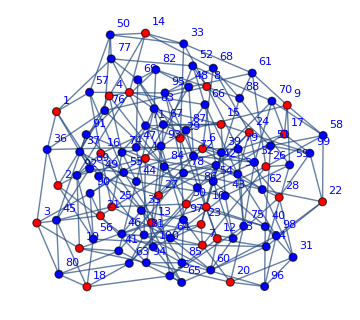

```mathematica
(*|2.2| Visualizing graph, identifying interesting nodes*)
AdjacencyGraph[Kij,VertexLabels->Automatic,VertexStyle->{x_/;x≤ g->Red,Blue},VertexSize->0.8, EdgeStyle->{Black,Thick}, ImageSize->Medium(*2300*)]
FindShortestPath[graph,1,2];(*use routine to find interesting nodes with suitable path lengths between them*)
perturbationNodes=(*Table[j,{j,n}]*){1};(*,3,13,19,20,22,28};*)(*perturbed oscillators, in ascending order*)
perturbationFrequencies=Table[10+j,{j,1}];
perturbationAmplitudes=Table[0.001+0.0005*j,{j,1}];
perturbationLags=Table[0.5*(j-1)^2,{j,1}];
outputNodes={1,2,3};(*{3,56,35,17,87,41}*);

perturbationVector=Table[0,{j,1,n}];
perturbationFrequenciesFull=Table[0,{j,n}];
perturbationLagsFull=Table[0,{j,n}];
Do[
perturbationVector[[perturbationNodes[[j]]]]=perturbationAmplitudes[[j]];
perturbationFrequenciesFull[[perturbationNodes[[j]]]]=perturbationFrequencies[[j]];
perturbationLagsFull[[perturbationNodes[[j]]]]=perturbationLags[[j]],
{j,Length[perturbationNodes]}];
(*Save["~/Desktop/draftTemp/test.dat",graph]*)(*save graph data*)
```

order Parameter=3.58982×10^-15

maximum angular difference=0.652474

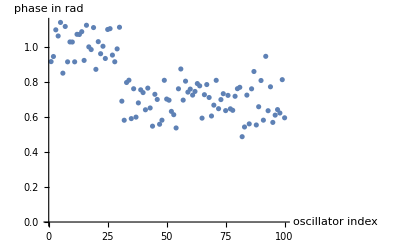

```mathematica
(*|3| Integrate oscillator dynamics on network to obtain stably locked phases (Euler scheme):*)
l=1;(*coupling strength*)
tMax=1000;(*integration steps*)
dt=0.1;(*integration step size*)
x=Table[RandomReal[{0,Pi/2}],{i,n}]; (*randomized vector of initial phases*)
ordPar=0;(*order parameter, should be practically zero at phaselocking*)
Do[
snX=Table[Sin[x[[i]]],{i,n}];(*table of sines*)
csnX=Table[Cos[x[[i]]],{i,n}];(*table of cosines*)
x2=p+l*(csnX*Kij.snX-snX*Kij.csnX);(*phase velocity*)
x+=dt*x2;(*Euler update rule*)
ordPar=Norm[x2],(*order parameter is scalar product of velocity vectors*)
{t,0,tMax,dt}];(*integrating for 0≤t≤tMax with time step dt*)
Print["order Parameter=",ordPar](*should be very close to zero in phase-locked state*)
Print["maximum angular difference=",Max[x]-Min[x]];(*bigger than Pi/2 for weak coupling?*)
ListPlot[x, AxesLabel->{"oscillator index","phase in rad"}]
```

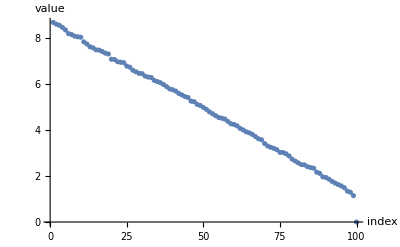

```mathematica
(*|3| Theoretically determine linear response functions:*)
(*|3.1| The math part in the article draft:*)
Mij=Table[-Kij[[i,j]]*(csnX[[i]]*csnX[[j]]+snX[[i]]*snX[[j]]),{i,n},{j,n}];(*only nontrivial block matrix of system's Jacobian*)
unitV=Table[1,{i,n}];(*unit vector for faster computation of ...*)
diagEl=-Mij.unitV;(*... vector of Mij's diagonal elements, Kii=0 assumed*)
Do[Mij[[i,i]]=diagEl[[i]],{i,1,n}];(*write Mij's diagonal elements*)
{eigenval,eigenvec}=Eigensystem[N[Mij]];
(*eigenvec=Eigensystem[Mij];(*matrix whose rows are Mij's eigenvectors*)
eigenval=Eigenvalues[Mij];(*Mij's eigenvalues, always exactly one zero-eigenvalue*)*)
ListPlot[eigenval,AxesLabel->{"index", "value"}](*plot Mij's eigenvalues, automatically ordered by absolute value*)
MijT=Inverse[Transpose[eigenvec]].Mij.Transpose[eigenvec];(*diagonalize Mij*)
LRfull:=DiagonalMatrix[Table[xsi[w,y,eigenval[[i]]],{i,1,n}]]
(*diagonal matrix whose elements are real parts of LRF in transformed coordinates*)
LRtrueFull:=Transpose[eigenvec].LRfull .Inverse[Transpose[eigenvec]];
(*matrix whose elements are real parts of LRF in initial coordinates*)
Total[LRtrueFull[[1]]];
Abs[LRtrueFull[[1,1]]/.w->perturbationFrequencies[[1]]/.y-> 1];
```

```mathematica
(*|4| Practically determine linear response functions with sinusoidal input:*)
tTrans=tMax-5000;(*transient time for Euler integration for fixed perturbation frequency*)
yPar=1;
linputNodes=Length[perturbationNodes];
loutputNodes=Length[outputNodes];
out=outputNodes[[1]];
xP=x; (*randomized vector of initial phases*)
vP=Table[0,{i,n}]; (*randomized vector of initial angular velocities*)
traceOut=List[];
maeElLRtrueFullAbs=Table[Abs[LRtrueFull[[out,j]]/.w->2/.y-> yPar],
{j,1,linputNodes}];
maeElLRtrueFullArg=Table[Arg[LRtrueFull[[out,j]]/.w->1/.y-> yPar],
{j,1,linputNodes}];
signOut=0;

Do[
snX=Table[Sin[xP[[i]]],{i,n}];(*table of sines*)
csnX=Table[Cos[xP[[i]]],{i,n}];(*table of cosines*)
vP2=-yPar*vP+p+l*(csnX*Kij.snX-snX*Kij.csnX)(*+Sin[t*dt*perturbationFrequenciesFull+perturbationLagsFull]perturbationVector*);
vP2[[1]]+=Sin[t*dt*perturbationFrequenciesFull[[1]]+perturbationLagsFull[[1]]+Pi]*perturbationVector[[1]];
xP+=dt*vP;(*Euler update rule I*)
vP+=dt*vP2;(*Euler update rule II*)
If[t>tTrans,
{signOut=0;
Do[
pertNo=perturbationNodes[[j]];pertAmp=perturbationAmplitudes[[j]];pertFreq=perturbationFrequencies[[j]];pertLa=perturbationLags[[j]];(*
vP2[[pertNo]]+=pertAmp*Sin[pertFreq* t* dt+pertLa];*)
signOut+=pertAmp*maeElLRtrueFullAbs[[pertNo]]*Sin[pertFreq*t*dt+pertLa+maeElLRtrueFullArg[[pertNo]]],
{j,1,linputNodes}];
outVector=Table[xP[[outputNodes[[j]]]]-x[[outputNodes[[j]]]],{j,loutputNodes}];
AppendTo[traceOut,Flatten[{t*dt,outVector,signOut}]]
}
],
{t,0,tMax,dt}];(*integrating for 0≤t≤tMax with time step dt*)
(*Write to file*)
Export["~/Desktop/draftTemp/test2.dat",traceOut];
```

$Aborted

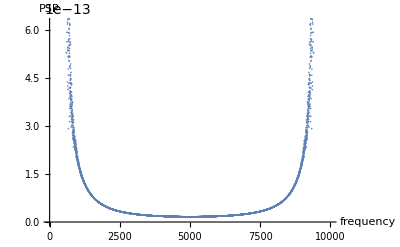

481.929

```mathematica
(*|5| Practically determine power spectra:*)
yParS=1; 
runs=10;(*runs to average over*)
tSteps=11000;
tTransS=1000;(*transient time for Euler integration*)
dtS=0.1;
dtSsqrt=N[Sqrt[dt]];
tWin=tSteps-tTransS;
loutputNodes=Length[outputNodes];
sXX=Table[0,{i,tWin},{j,loutputNodes}];
SetSharedVariable[sXX];
sXX2=Table[0,{i,tWin}];
SetSharedVariable[sXX2];

Do[
noiseMatrix=Table[0,{i,n},{j,tSteps}];
Do[
noiseAux=RandomFunction[ WhiteNoiseProcess[0.001],{IntegerPart[tSteps]}];
noiseAux2=noiseAux["Values"];
noiseMatrix[[perturbationNodes[[j]]]]=noiseAux2,
{j,Length[perturbationNodes]}];
xS=x;(*Table[RandomReal[{0,Pi/2}],{i,n}];*) (*randomized vector of initial phases*)
vS=Table[0(*RandomReal[{-1,1}]*),{i,n}]; (*randomized vector of initial angular velocities*)
xT=0;
vT=0;
tSeries=List[];

Do[
snX=Table[Sin[xS[[i]]],{i,n}];(*table of sines*)
csnX=Table[Cos[xS[[i]]],{i,n}];(*table of cosines*)
vS2=-yParS*vS+p+l*(csnX*Kij.snX-snX*Kij.csnX);
xS+=dt*vS;(*Euler update rule I*)
vS+=dt*vS2+dtSsqrt*noiseMatrix[[All,t]];(*Euler update rule II with white Noise*)

(*xTb=xT;
xT+=dt*(-yParS*xT)+dtSsqrt*noiseMatrix[[1,t]];*)
(*xT+=dt*vT;
vT+=dt*(-yParS*vT-1*xTb)+dtSsqrt*noiseAux2[[t]];*)
(*xT=noiseAux2[[t]];noiseMatrix[[perturbationNodes[[1]],t]];*)
If[t>   tTransS,AppendTo[tSeries,xS[[3]]](*{outVector=Table[xS[[outputNodes[[j]]]],{j,loutputNodes}],AppendTo[tSeries,Flatten[outVector]]}*)],
{t,tSteps}];
ft=Fourier[tSeries];
ftCC=Conjugate[ft];
sXX2+=ft*ftCC,
{runIndex,runs}];
ListPlot[ Re[dt*sXX2]/runs,AxesLabel->{"frequency", "PSP"}]
 Re[dt*sXX2[[1]]]/runs
(*{runIndex,runs}];*)
(*ListPlot[tSeries[[All,1]]]
ft=Fourier[tSeries[[All,1]]];
ftCC=Conjugate[ft];
sXX[[All,1]]=Re[ft*ftCC];
ListPlot[sXX[[All,1]]]*)
(*{runIndex,runs}];*)
(*Write to file*)
Export["~/Desktop/draftTemp/spectra.dat",sXX];
```